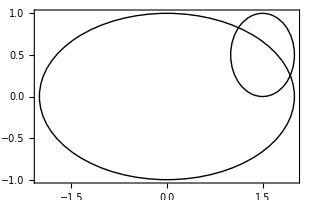

```mathematica
Graphics[{
Circle[{0,0},{2,1}],
Circle[{3/2,1/2},1/2]
},PlotRange->{{-2,2},{-1,1}},Frame->True]
```

```mathematica
ℛ=RegionIntersection[Disk[{0,0},{2,1}],Disk[{2-xr,1-xr},xr]];
```

```mathematica
r=Area[ℛ,Assumptions->{0<xr<1}];
```

$Aborted

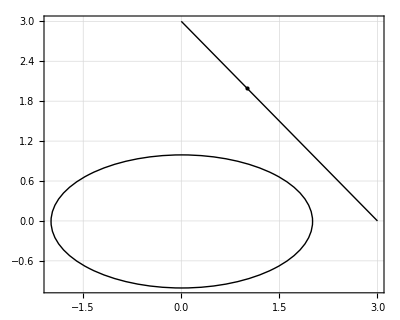

```mathematica
Graphics[{
Circle[{0,0},{2,1}],
Line[{{0,3},{3,0}}],
{PointSize[Large],Point[{1,2}]}
},
PlotRange->{{-2,3},{-1,3}},
Frame->True,
GridLines->Automatic]
```

```mathematica
Manipulate[
Graphics[{
Circle[{0,0},{2,1}],
Line[{{0,3},{3,0}}],
Point[{1,2}],
Circle[{1,2},r]
},
PlotRange->{{-2,3},{-1,3}},
Frame->True,
GridLines->Automatic],
{r,0,2}
]
```

```mathematica
Solve[(x-1)^2+(y-2)^2==r^2,y]
```

{{y→2-√(-1+r^2+2 x-x^2)},{y→2+√(-1+r^2+2 x-x^2)}}

```mathematica
distance[{x1_,y1_},{x2_,y2_}]:=√((x1-x2)^2+(y1-y2)^2);
```

```mathematica
slope[{x1_,y1_},{x2_,y2_}]:=(y1-y2)/(x1-x2);
```

```mathematica
result=Solve[{
D[√(1-Subscript[t, x]^2/4),Subscript[t, x]]slope[{1,2},{Subscript[t, x],Subscript[t, y]}]==-1,
Subscript[t, y]==√(1-Subscript[t, x]^2/4)
},{Subscript[t, x],Subscript[t, y]}]//FullSimplify;
```

```mathematica
result
```

{{t_x→1/3 (2-√13+√(1+4 √13)),t_y→1/6 (-2+√13+√(1+4 √13))}}

```mathematica
distance[{1/3 (2-√13+√(1+4 √13)),1/6 (-2+√13+√(1+4 √13))},{1,2}]//FullSimplify
```

√(1/6 (45-√(673+208 √13)))

```mathematica
√(1/6 (45-√(673+208 √13)))//N
```

1.10136

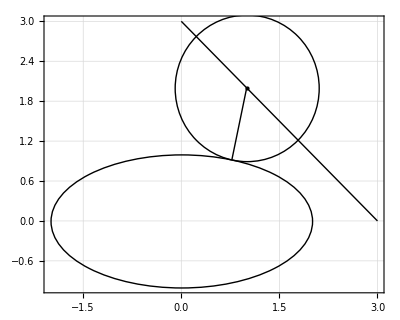

```mathematica
Graphics[{
Circle[{0,0},{2,1}],
Line[{{0,3},{3,0}}],
Point[{1,2}],
Circle[{1,2},√(1/6 (45-√(673+208 √13)))],
Line[{{1/3 (2-√13+√(1+4 √13)),1/6 (-2+√13+√(1+4 √13))},{1,2}}]
},
PlotRange->{{-2,3},{-1,3}},
Frame->True,
GridLines->Automatic]
```

```mathematica
{3,0}+t({0,3}-{3,0})
```

{3-3 t,3 t}

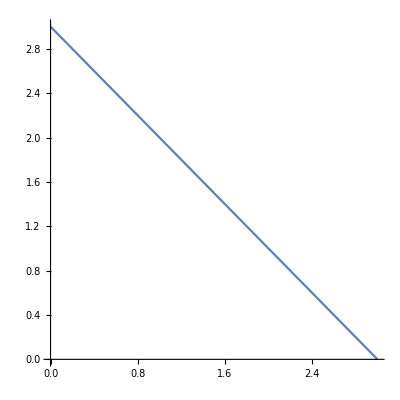

```mathematica
ParametricPlot[{3-3 t,3 t},{t,0,1}]
```

```mathematica
result=Solve[{
D[√(1-Subscript[t, x]^2/4),Subscript[t, x]]slope[{3-3 t,3 t},{Subscript[t, x],Subscript[t, y]}]==-1,
Subscript[t, y]==√(1-Subscript[t, x]^2/4)
},{Subscript[t, x],Subscript[t, y]},Assumptions->{0<=t<=1,{Subscript[t, x],Subscript[t, y]}∈Reals}]//FullSimplify//Flatten//{Subscript[t, x],Subscript[t, y]}/.#&
```

{Root[-64+128 t-64 t^2+(32-32 t) #1+(12-32 t+20 t^2) #1^2+(-8+8 t) #1^3+#1^4&,2],1/2 √(4-Root[-64+128 t-64 t^2+(32-32 t) #1+(12-32 t+20 t^2) #1^2+(-8+8 t) #1^3+#1^4&,2]^2)}

```mathematica
Solve[{3-3 t,3 t}=={1,2},t]
```

{{t→2/3}}

```mathematica
resultF[t_]:={Root[-64+128 t-64 t^2+(32-32 t) #1+(12-32 t+20 t^2) #1^2+(-8+8 t) #1^3+#1^4&,2],1/2 √(4-Root[-64+128 t-64 t^2+(32-32 t) #1+(12-32 t+20 t^2) #1^2+(-8+8 t) #1^3+#1^4&,2]^2)};
```

```mathematica
Manipulate[
Module[{circleO,circleR,tangentP},
circleO={3-3 t,3 t};
tangentP=resultF[t];
circleR=distance[circleO,tangentP];
Graphics[{
Circle[{0,0},{2,1}],
Line[{{0,3},{3,0}}],
Point[circleO],
Circle[circleO,circleR],
Point[tangentP]
},
PlotRange->{{-2,3},{-1,3}},
Frame->True,
GridLines->Automatic]
],
{t,0,1},
SaveDefinitions->True
]
```

```mathematica
result
```

{Root[-64+128 t-64 t^2+(32-32 t) #1+(12-32 t+20 t^2) #1^2+(-8+8 t) #1^3+#1^4&,2],1/2 √(4-Root[-64+128 t-64 t^2+(32-32 t) #1+(12-32 t+20 t^2) #1^2+(-8+8 t) #1^3+#1^4&,2]^2)}

```mathematica
Manipulate[
Module[{},Evaluate[result/.t->t]],
{t,0,1}
]
```

```mathematica
2/3//N
```

0.666667

```mathematica
resultF[2/3]
```

{2,0}